## 1 - export of velocity only

```mathematica
SetDirectory["~/Documents/Processing/MIDIDance"];
data=Import["test1.txt","CSV"];
```

```mathematica
Dimensions@data
```

{210,9}

What fraction of hits was id. correctly?

```mathematica
nrSignals=6;
Total[If[#⟦2⟧==#⟦3⟧,1,0]&/@data]
(N@%)/(Length@data)
```

172

0.819048

What fraction of correct hits was there for each axis?

```mathematica
CorrectFraction[data_List]:=(N@Total[If[#⟦2⟧==#⟦3⟧,1,0]&/@data])/(Length@data);
```

```mathematica
CorrectFraction[Cases[data,{_,_,#,__}]]&/@Range[0,nrSignals-1]
```

{1.,1.,0.683544,0.793103,1.,1.}

How do the velocity values cluster?

```mathematica
ListPointPlot3D[Cases[data,{_,_,#,__}]⟦All,4;;6⟧&/@{0,1,2,-1},PlotRange->{{0,1},{0,1},{0,1}},AspectRatio->1,PlotStyle->{Red,Darker@Green,Blue,Black}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Cases[data,{_,#,2,__}]⟦All,4;;6⟧&/@{2,0,1},PlotRange->{{0,1},{0,1}},AspectRatio->1,PlotStyle->{Green,Red,Red,Black}]
```

## 2 - export of vector of past values

```mathematica
SetDirectory["~/Documents/Processing/MIDIDance"];
data=Import["test1-max.txt","CSV"];
```

```mathematica
(* detect the length of the vector of past values *)
nrSignals=6;
lengthSignals=(Length[First@data]-3)/nrSignals
```

3

```mathematica
(* separate data sets for different axis *)
xdatasep=({#⟦2;;3⟧,Partition[#⟦4;;-1⟧,lengthSignals]}&/@data);
```

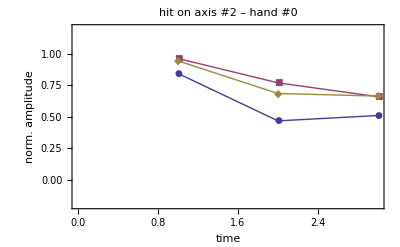

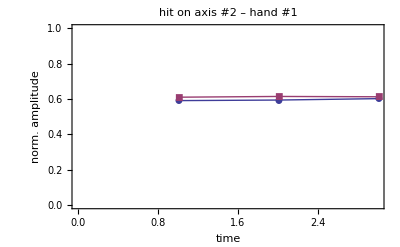

```mathematica
temp=Last@Transpose@Cases[xdatasep,{{_,axis=2},__}];
ListPlot[Mean[temp]⟦1;;3⟧,Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. amplitude"},PlotRange->{-0.2,1.2},PlotLabel->"hit on axis #"<>ToString@axis<>" – hand #0"]
ListPlot[Mean[temp]⟦4;;6⟧,Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. amplitude"},PlotRange->{0,1},PlotLabel->"hit on axis #"<>ToString@axis<>" – hand #1"]
```

```mathematica
rangeOfHand={1;;3,4;;6};
GraphicsGrid[
Table[ListPlot[Mean[Last@Transpose@Cases[xdatasep,{{_,axisID+3*handID},__}]]⟦rangeOfHand⟦handID+1⟧⟧,Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. ampl."},PlotRange->{-0.2,1.2},PlotLabel->"hand #"<>ToString[handID]<>": hit on axis #"<>ToString[axisID+3*handID],ImageSize->200],{handID,0,1},{axisID,0,2}],
ImageSize->1000
]
```

## 3 - different trials of post value vectors (“Rinse & repeat”)

```mathematica
SetDirectory["~/Documents/Processing/MIDIDance/RinseAndRepeat"];
nrSignals=6;
```

```mathematica
ImportProcessingHitOutput[filename_String,nrSignals_Integer]:=Module[{data,lengthSignals,xdatasep},
data=Import[filename,"CSV"];
lengthSignals=(Length[First@data]-3)/nrSignals;
xdatasep=({#⟦2;;3⟧,Partition[#⟦4;;-1⟧,lengthSignals]}&/@data);
Return[xdatasep]
];
```

```mathematica
filelist=FileNames["*.txt"];
signallist={};
Do[
AppendTo[signallist,ImportProcessingHitOutput[fname,nrSignals]];
Print["Loaded file '"<>fname<>"'."];
,{fname,filelist}]
```

Loaded file 'test1.txt'.

Loaded file 'test2.txt'.

Loaded file 'test3.txt'.

Loaded file 'test4.txt'.

Loaded file 'test5.txt'.

```mathematica
xplots={};
trange=1;;15;
trial=0;
Do[
meantraces=Last@Transpose@Cases[data,{{axis=2,_},__}];
actualplot=ListPlot[Mean[meantraces]⟦1;;3,trange⟧,Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. amplitude"},PlotRange->{-0.2,1.2},PlotLabel->"actual hit on axis #"<>ToString@axis<>"\nhand #0, trial #"<>ToString[trial]];
meantraces=Last@Transpose@Cases[data,{{_,axis},__}];
shouldhavebeenplot=ListPlot[Mean[meantraces]⟦1;;3,trange⟧,Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. amplitude"},PlotRange->{-0.2,1.2},PlotLabel->"should have been hit on axis #"<>ToString@axis<>"\nhand #0, trial #"<>ToString[trial++]];

AppendTo[xplots,{actualplot,shouldhavebeenplot}];
,{data,signallist}];
Clear[meantraces,actualplot,shouldhavebeenplot];
GraphicsGrid[xplots,ImageSize->700]
```

#### Recordings across trials

```mathematica
alldata=Flatten[signallist,1];
```

```mathematica
recordedSituatons=Union@alldata⟦All,1⟧
```

{{0,-1},{0,0},{0,2},{0,3},{1,-1},{1,0},{1,1},{1,2},{1,3},{2,0},{2,2},{3,-1},{3,3},{3,4},{3,5},{4,-1},{4,3},{4,4},{4,5},{5,-1},{5,3},{5,5}}

```mathematica
RecordingsWithAxis[datasep_List,axisActual_,axisTarget_]:=Last@Transpose@Cases[datasep,{{axisActual,axisTarget},__}];
RecordingsActualAxis[datasep_List,axis_Integer]:=RecordingsWithAxis[datasep,axis,_];
RecordingsTargetAxis[datasep_List,axis_Integer]:=RecordingsWithAxis[datasep,_,axis];
CorrectFraction[datasep_List,axis_Integer]:=Module[{nrTargettingThisAxis,nrTargettingAndHittingThisAxis,f=0},
nrTargettingThisAxis=Length@RecordingsTargetAxis[datasep,axis];
If[nrTargettingThisAxis>0,
nrTargettingAndHittingThisAxis=Length@RecordingsWithAxis[datasep,axis,axis];
f=nrTargettingAndHittingThisAxis/nrTargettingThisAxis;
];
Return[f];
];
```

```mathematica
rangeOfHand={1;;3,4;;6};
trange={0,14.5};
GraphicsGrid[
Table[ListPlot[Mean[xd=RecordingsActualAxis[alldata,axisID+3*handID]⟦All,rangeOfHand⟦handID+1⟧⟧],Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. ampl."},PlotRange->{trange,{0.2,1.2}},PlotLabel->"hand #"<>ToString[handID]<>": actual hit on axis #"<>ToString[axisID+3*handID]<>"\nN = "<>ToString[Length@xd],ImageSize->200],{handID,0,1},{axisID,0,2}],
ImageSize->1000
]

GraphicsGrid[
Table[ListPlot[Mean[xd=RecordingsTargetAxis[alldata,xa=axisID+3*handID]⟦All,rangeOfHand⟦handID+1⟧⟧],Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. ampl."},PlotRange->{trange,{0.2,1.2}},PlotLabel->"hand #"<>ToString[handID]<>": target hit on axis #"<>ToString[axisID+3*handID]<>"\nN = "<>ToString[Length@xd]<>", "<>ToString@Round[100.0*CorrectFraction[alldata,xa]]<>"% correct",ImageSize->200],{handID,0,1},{axisID,0,2}],
ImageSize->1000
]
Clear[xd,xa];
```

#### What is the trial-by-trial variability like?

```mathematica
trange={0,14.5};
ListPlot[RecordingsWithAxis[alldata,axis=0,axis]⟦All,plotaxis=1⟧,Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. ampl."},PlotRange->{trange,{0.2,1.2}},PlotLabel->""]
ListPlot[RecordingsTargetAxis[alldata,axis]⟦All,plotaxis⟧,Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. ampl."},PlotRange->{trange,{0.2,1.2}},PlotLabel->""]
```

```mathematica
ListPlot[RecordingsTargetAxis[alldata,-1]⟦All,plotaxis⟧,Joined->True,PlotMarkers->Automatic,FrameLabel->{"time","norm. ampl."},PlotRange->{trange,{0.2,1.2}},PlotLabel->""]
```

#### Is it possible to increase accuracy by Bayesian inference?

```mathematica
(* 1. Calculate mean and standard deviation of the correct trajectories for each outcome *)
means=stddevs={};
For[outcome=-1,outcome<nrSignals,outcome++,
AppendTo[means,{outcome,Mean@RecordingsTargetAxis[alldata,outcome]}];
AppendTo[stddevs,{outcome,StandardDeviation/@Transpose[RecordingsTargetAxis[alldata,outcome]]}];
];
```

```mathematica
means⟦1⟧
stddevs⟦1⟧
```

{-1,{{0.669932,0.628594,0.629503,0.634433,0.636967,0.633937,0.633295,0.63132,0.633052,0.636771,0.652647,0.668176,0.679797,0.67705,0.652169,0.639722,0.633411,0.632904,0.631473,0.631955,0.63071,0.631653,0.628777,0.630903,0.631003,0.633936,0.638912,0.644204,0.647094,0.654776},{0.804098,0.768945,0.760183,0.762731,0.767375,0.763887,0.760704,0.761823,0.76676,0.769956,0.779107,0.781921,0.790291,0.789889,0.771711,0.763705,0.766993,0.768685,0.764579,0.766322,0.767207,0.766242,0.768081,0.764054,0.765043,0.773726,0.778294,0.781617,0.783505,0.785554},{0.932762,0.90489,0.894579,0.884792,0.879195,0.875214,0.875923,0.873172,0.873852,0.884747,0.907344,0.929202,0.956553,0.939955,0.916241,0.899837,0.888044,0.888106,0.883519,0.883439,0.884985,0.883924,0.880483,0.884758,0.889642,0.888467,0.89332,0.900881,0.906959,0.914002},{0.713163,0.458017,0.438763,0.475802,0.523785,0.54703,0.554397,0.556956,0.563265,0.564392,0.565568,0.568177,0.569443,0.574293,0.586112,0.60337,0.622979,0.624889,0.589193,0.559052,0.560362,0.5615,0.56769,0.590041,0.609647,0.649448,0.661212,0.694691,0.690843,0.672596},{0.518679,0.745823,0.825343,0.771567,0.699101,0.675914,0.668619,0.665935,0.662381,0.661687,0.67083,0.67484,0.675504,0.663025,0.645017,0.628228,0.62946,0.627683,0.666354,0.688295,0.687618,0.673167,0.670638,0.660148,0.648205,0.607489,0.632498,0.653361,0.652167,0.617923},{0.820716,0.723148,0.750773,0.829172,0.87157,0.887797,0.903221,0.917337,0.929468,0.943937,0.954274,0.967937,0.976418,0.9836,0.977986,0.966882,0.95354,0.914306,0.876195,0.863489,0.87291,0.882304,0.88928,0.912863,0.939059,0.951274,0.961099,0.97536,0.953587,0.907446}}}

{-1,{{0.113973,0.0311562,0.0198984,0.0192269,0.0212624,0.0219862,0.025401,0.0264821,0.0301064,0.0316231,0.0439891,0.0469187,0.0656975,0.0629366,0.0518807,0.0525806,0.0381332,0.0331536,0.0295617,0.0300047,0.029993,0.0299773,0.0253433,0.0212795,0.0253114,0.0250253,0.0270691,0.0301471,0.0385289,0.0569686},{0.0576578,0.0344572,0.0366717,0.0346863,0.0270918,0.0219135,0.021359,0.0239472,0.0298824,0.028149,0.0365985,0.0435513,0.0514842,0.0643609,0.0402436,0.0499778,0.0323006,0.038759,0.0307097,0.0294473,0.026879,0.0257246,0.0260202,0.0265398,0.0301476,0.0304633,0.0262772,0.0256526,0.0311017,0.0252422},{0.0802306,0.0287639,0.0146613,0.0171495,0.0175009,0.0198265,0.0222309,0.0281136,0.0265386,0.0294622,0.0584294,0.0656782,0.0804171,0.0694828,0.0573577,0.0625634,0.0491134,0.0456103,0.0296362,0.0260719,0.0223136,0.0194164,0.0208475,0.0224157,0.0235374,0.0238812,0.0193603,0.0213993,0.035325,0.0458},{0.270908,0.15679,0.140681,0.107444,0.0570615,0.0361452,0.0370121,0.0340398,0.0335484,0.0372594,0.0400242,0.0330206,0.028474,0.0294234,0.0354334,0.0715752,0.114029,0.136315,0.0590684,0.0726108,0.0506724,0.0543846,0.0701217,0.0922625,0.119615,0.159368,0.193328,0.198362,0.212099,0.248095},{0.258711,0.17933,0.174026,0.131472,0.0775689,0.0469715,0.0380727,0.0390609,0.0381462,0.0405064,0.0437574,0.0363399,0.0366282,0.049647,0.0886297,0.130696,0.128732,0.139619,0.0742108,0.106508,0.0946476,0.0718874,0.095253,0.116752,0.146452,0.196943,0.197254,0.22051,0.247894,0.247766},{0.262093,0.244734,0.18435,0.133809,0.0949668,0.0702852,0.0569299,0.0495526,0.0514144,0.0605915,0.0669447,0.0630257,0.0741182,0.0986148,0.0995745,0.0957438,0.0915099,0.0878245,0.155844,0.165678,0.135154,0.120028,0.113907,0.106585,0.134683,0.194479,0.228762,0.195082,0.175153,0.242197}}}

```mathematica
(* In a first iteration, we take the time steps to be statistically independent and take for P(θ|d) simply the product distribution with mean and standard deviation as computed above *)
```

```mathematica
0.7/6
```

0.116667

```mathematica
1-0.7
```

0.3

```mathematica
PDF[NormalDistribution[0,1],0]
```

1/(√(2 π))

```mathematica
BayesianProbability[trajectory_List,outcomes_List,nrSignals_Integer,meanslist_List,stddevslist_List]:=Module[{p,mean,dev,result,i},
result={};
Do[
mean=Last@First@Cases[meanslist,{oo,__}];
dev=Last@First@Cases[stddevslist,{oo,__}];
p=1.0;
Do[
p+=Log[PDF[NormalDistribution[#⟦1⟧,#⟦2⟧],#⟦3⟧]]&/@Transpose[{mean⟦axisindex⟧,dev⟦axisindex⟧,trajectory⟦axisindex⟧}];
,{axisindex,Length@mean}];
AppendTo[result,{oo,p}];
,{oo,outcomes}];
Return[result];
];
```

```mathematica
exampletrace=Last[xtemp=alldata⟦10⟧];
First@xtemp
```

{1,1}

```mathematica
xtemp=BayesianProbability[exampletrace,Range[-1,nrSignals-1,1],nrSignals,means,stddevs]
```

{{-1,-409.532},{0,137.152},{1,260.458},{2,179.553},{3,-102.245},{4,-1519.61},{5,-863.046}}

```mathematica
BayesianResult@xtemp
```

1

```mathematica
Ordering@xtemp⟦All,-1⟧
Flatten@Position[RankOrder@xtemp⟦All,-1⟧,7]
```

{1,6,7,5,3,4,2}

{2}

```mathematica
BayesianResult[bpresult_List]:=Module[{ranking},Return@First@bpresult⟦First@Flatten@Position[ranking=RankOrder@Last@Transpose@bpresult,Max@ranking]⟧];
```

```mathematica
traditionalMatching=alldata⟦All,1⟧;
traditionalAccuracy=N@Count[traditionalMatching,{x_,x_}]/Length[traditionalMatching]
```

0.62982

```mathematica
bayesianMatching={#⟦1,2⟧,BayesianResult@BayesianProbability[Last@#,Range[-1,nrSignals-1,1],nrSignals,means,stddevs]}&/@alldata;
```

```mathematica
bayesianMatching
```

```mathematica
bayesianAccuracy=N@Count[bayesianMatching,{x_,x_}]/Length[bayesianMatching]
```

0.966581

```mathematica
BarChart[{traditionalAccuracy,bayesianAccuracy},ChartLegends->{"traditional (velocity)","Bayesian"},Frame->True,FrameLabel->{"method","prediction accuracy"},PlotRange->{0,1},FrameTicks->{False,True},ChartStyle->StandardColors]
```